Berechnung für Praktikumsversuch Quantisierter Leitwert
Erst Daten importieren, dann Sachen berechnen und Bilder exportieren.

```mathematica
(* Importiere Daten von Widerstandsbox *)
Ohm100 =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/100ohm.dat","FieldSeparators"->","];
Ohm1k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/1000ohm.dat","FieldSeparators"->","];
Ohm10k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/10kOhm.dat","FieldSeparators"->","];
Ohm100k =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/100kOhm.dat","FieldSeparators"->","];
Ohm1M =Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/1MOhm.dat","FieldSeparators"->","];

(* Berechne Mittel der Widerstände (6 Messwerte) *)
a =Sum[1/Sqrt[Ohm100[[n,1]]^2+Ohm100[[n,2]]^2],{n,Length[Ohm100]}]/Length[Ohm100];
b =Sum[1/Sqrt[Ohm1k[[n,1]]^2+Ohm1k[[n,2]]^2],{n,Length[Ohm1k]}]/Length[Ohm1k];
c =Sum[1/Sqrt[Ohm10k[[n,1]]^2+Ohm10k[[n,2]]^2],{n,Length[Ohm10k]}]/Length[Ohm10k];
d =Sum[1/Sqrt[Ohm100k[[n,1]]^2+Ohm100k[[n,2]]^2],{n,Length[Ohm100k]}]/Length[Ohm100k];
e =Sum[1/Sqrt[Ohm1M[[n,1]]^2+Ohm1M[[n,2]]^2],{n,Length[Ohm1M]}]/Length[Ohm1M];

(* linearer Fit mit Auswertung *)
data = {{100,a},{1000,b},{10000,c},{100000,d},{1000000,e}};
errors = {0.1,1,10,1000,10000};
lm = LinearModelFit[data,x,x,Weights->errors];
PlotBox=Show[ListPlot[data,PlotRange->Full],Plot[lm[x],{x,0,1000000},PlotStyle->Orange],ImageSize->Large, AxesLabel->{"R_theo in Ω","R_exp in Ω"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]

(* Exportiere als .eps Vektorgrafik *)
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/box.eps",PlotBox]

(* Parameter des Fits *)
lm["ParameterTable"]
lm["AdjustedRSquared"]
PearsonChiSquareTest[data]
```

Import::nffil: File not found during Import.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

General::stop: Further output of LinearModelFit::notdata will be suppressed during this calculation.

-Graphics-

Export::nodir: Directory C:\Users\chegerland\Desktop\Praktikum_QL\Protokoll\Berechnung-Bilder\ does not exist.

Export::noopen: Cannot open /Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/box.eps.

$Failed

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

LinearModelFit[{{100,Indeterminate},{1000,Indeterminate},{10000,Indeterminate},{100000,Indeterminate},{1000000,Indeterminate}},x,x,Weights→{0.1,1,10,1000,10000}][ParameterTable]

LinearModelFit[{{100,Indeterminate},{1000,Indeterminate},{10000,Indeterminate},{100000,Indeterminate},{1000000,Indeterminate}},x,x,Weights→{0.1,1,10,1000,10000}][AdjustedRSquared]

PearsonChiSquareTest::rctnln: The argument {{100,Indeterminate},{1000,Indeterminate},{10000,Indeterminate},{100000,Indeterminate},{1000000,Indeterminate}} at position 1 should be a rectangular array of real numbers with length greater than the dimension of the array.

PearsonChiSquareTest[{{100,Indeterminate},{1000,Indeterminate},{10000,Indeterminate},{100000,Indeterminate},{1000000,Indeterminate}}]

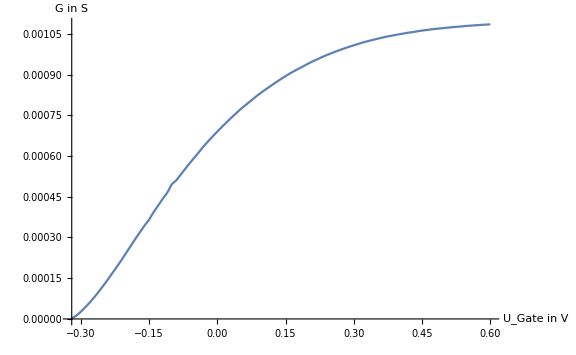

/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/g.eps

```mathematica
(* Importiere Struktur G *)
G = Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/G.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
(* korrigiere Leitwerte um Abweichung aus Widerstandsbox *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,G[[n,1]]],{n,Length[G]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[G[[n,2]]^2 + G[[n,3]]^2  ]],{n,Length[G]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
PlotG =ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate in V","G in S"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/g.eps",PlotG]
```

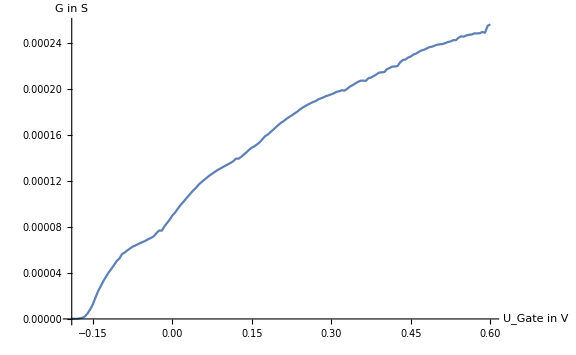

/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/j.eps

```mathematica
(* Importiere Struktur I*)
J= Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/QL_I.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,J[[n,1]]],{n,Length[J]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[J[[n,2]]^2 + J[[n,3]]^2  ]],{n,Length[J]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
PlotJ = ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate in V","G in S"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/j.eps",PlotJ]
```

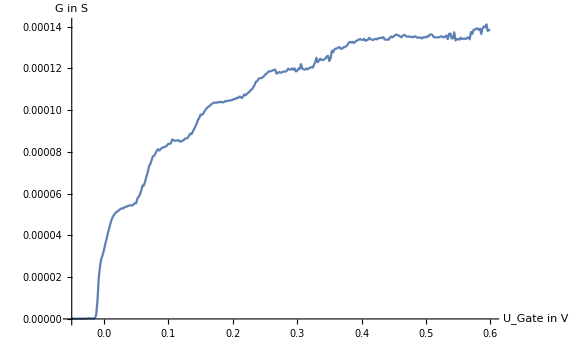

/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/l.eps

```mathematica
(* Importiere Struktur L*)
L = Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/L.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,L[[n,1]]],{n,Length[L]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[L[[n,2]]^2 + L[[n,3]]^2  ]],{n,Length[L]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
PlotL = ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate in V","G in S"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/l.eps",PlotL]
```

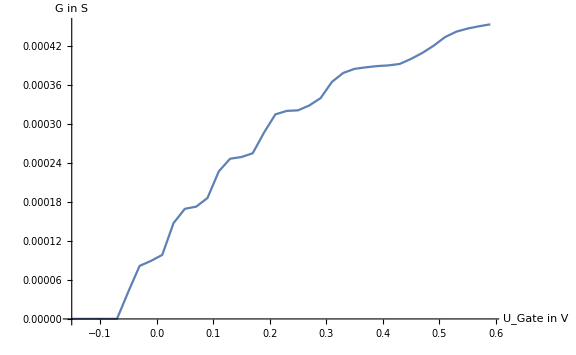

/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/lfein.eps

```mathematica
(* Importiere Struktur L_fein*)
Lfein= Import["/Users/chegerland/Desktop/Praktikum_QL/Messung/Lfein.dat","FieldSeparators"->","];

(* Lege Arrays für Spannungen und Leitwerte an *)
Spannungen = {};
Do[Spannungen=Append[Spannungen,Lfein[[n,1]]],{n,Length[Lfein]}];
Leitwerte = {};
Do[Leitwerte=Append[Leitwerte,Sqrt[Lfein[[n,2]]^2 + Lfein[[n,3]]^2  ]],{n,Length[Lfein]}]
data2 = Transpose[{Spannungen,Leitwerte}];

(* Plot *)
PlotLfein = ListPlot[data2,Joined->True, AxesOrigin->{Min[Spannungen],0},ImageSize->Large, AxesLabel->{"U_Gate in V","G in S"},TicksStyle->Directive[Black, 14],LabelStyle->Directive[Black, 14]]
Export["/Users/chegerland/Desktop/Praktikum_QL/Protokoll/Berechnung-Bilder/lfein.eps",PlotLfein]
```